```mathematica
t=.
```

```mathematica
(*x''[t] == (-g x'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2]*)
(*y''[t] == -g (1 + (y'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2])*)
V  = 30
θ  = (50 × π) / 180
c = 3 10^8
g = 9.8
vt = 135
sol = NDSolve[ {x''[t] == (-g x'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2],y''[t] == -g (1 + (y'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2]),x[0]==0.0,x'[0]==V Cos[θ],y[0]==2,y'[0]==V Sin[θ]}, {x, y}, {t, 0, 200} ]
```

30

(5 π)/18

300000000

9.8

135

{{x→InterpolatingFunction[{{0.,200.}},<>],y→InterpolatingFunction[{{0.,200.}},<>]}}

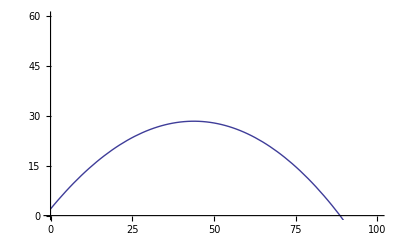

```mathematica
myplot = ParametricPlot[Evaluate[{x[t],y[t]}/.sol],{t,0,200},PlotRange-> {{0,100},{0,60}}]
```

```mathematica
Manipulate[
g = 9.8;
Module[{result=NDSolve[{x''[t]==(-g x'[t]/vt^2.0) Sqrt[x'[t]^2.0+y'[t]^2.0],y''[t]==-g (1.0+(y'[t]/vt^2.0) Sqrt[x'[t]^2.0+y'[t]^2.0]),
x[0]==0.0,x'[0]==v0 Cos[θ],y[0]==2.0,y'[0]==v0 Sin[θ]},{x,y},{t,0,tf}]},

ParametricPlot[ {{v0 Cos[θ] t},{h0+v0 Sin[θ] t-(1/2) g t^2 },{Evaluate[ {x[t],y[t] }/.result] }},{t,0,tf },AxesLabel-> {"x (m)","y (m)"},PlotStyle->{{Blue},{Red}},PlotRange -> {{0, 2000}, {-10, 100}},PlotRange->All, ImageSize -> {1100, 300}]],

{{v0,439,"Initial Velocity (m/s)"},0,500,Appearance->"Labeled"},
{{θ,15*π/180,"Launch Angle (rad)"},0.017,π/2,Appearance->"Labeled"},{{vt,135,"Terminal Velocity (m/s)"},0.5,150.0,Appearance->"Labeled"},
{{h0, 1,"Launch Height (m)"},0,2,Appearance -> "Labeled"},
{{tf,200,"Time (s)"},0,200,Appearance->"Labeled"}]
```